```mathematica
Get["~/projects/nrmma/nrmma.m"]
```

```mathematica
coordX=ReadMinTrackerCoordinate["J5.25_17c",0,1]
```

Reading...

DataTable[...]

```mathematica
coordY=ReadMinTrackerCoordinate["J5.25_17c",0,2]
```

DataTable[...]

```mathematica
ReadPsi4["J5.25_17c",2,2,70]
```

DataTable[...]

```mathematica
coords=ReadMinTrackerCoordinates["J5.25_17c",0]
```

DataTable[...]

```mathematica
coordX
```

DataTable[...]

```mathematica
coordY
```

DataTable[...]

```mathematica
ph=ReadMinTrackerPhase["J5.25_17c"]
```

Reading...

Reading...

DataTable[...]

```mathematica
sinSquared=MakeDataTable[Table[{t,Sin[t]^2},{t,0,2Pi,0.1}]]
```

DataTable[...]

```mathematica
cosSquared=MakeDataTable[Table[{t,Cos[t]^2},{t,0,2Pi,0.1}]]
```

DataTable[...]

```mathematica
three=MakeDataTable[Table[{t,3},{t,0,2Pi,0.1}]]
```

DataTable[...]

```mathematica
sum=sinSquared+cosSquared
```

DataTable[...]

```mathematica
sum3=sinSquared+cosSquared+three
```

DataTable[...]

```mathematica
diff=sinSquared-cosSquared
```

DataTable[...]

```mathematica
minusSinSquared=-sinSquared
```

-DataTable[...]

```mathematica
twoSinSquared=2 sinSquared
```

DataTable[...]

```mathematica
ToList[twoSinSquared]
```

{{0.,0.},{0.1,0.0199334},{0.2,0.078939},{0.3,0.174664},{0.4,0.303293},{0.5,0.459698},{0.6,0.637642},{0.7,0.830033},{0.8,1.0292},{0.9,1.2272},{1.,1.41615},{1.1,1.5885},{1.2,1.73739},{1.3,1.85689},{1.4,1.94222},{1.5,1.98999},{1.6,1.99829},{1.7,1.9668},{1.8,1.89676},{1.9,1.79097},{2.,1.65364},{2.1,1.49026},{2.2,1.30733},{2.3,1.11215},{2.4,0.912501},{2.5,0.716338},{2.6,0.531483},{2.7,0.365307},{2.8,0.224434},{2.9,0.11448},{3.,0.0398297},{3.1,0.0034579},{3.2,0.00681508},{3.3,0.0497674},{3.4,0.130603},{3.5,0.246098},{3.6,0.391649},{3.7,0.561453},{3.8,0.74874},{3.9,0.946045},{4.,1.1455},{4.1,1.33915},{4.2,1.51929},{4.3,1.67872},{4.4,1.81109},{4.5,1.91113},{4.6,1.97484},{4.7,1.99969},{4.8,1.98469},{4.9,1.93043},{5.,1.83907},{5.1,1.71427},{5.2,1.56098},{5.3,1.38534},{5.4,1.19433},{5.5,0.995574},{5.6,0.796995},{5.7,0.606509},{5.8,0.43171},{5.9,0.279568},{6.,0.156146},{6.1,0.0663664},{6.2,0.0138077}}

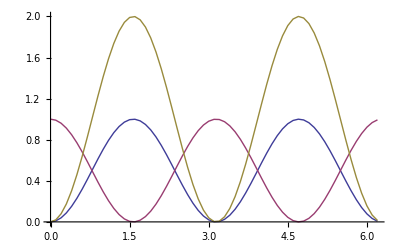

```mathematica
ListLinePlot[{sinSquared,cosSquared,twoSinSquared}]
```

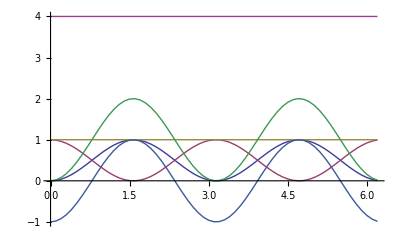

```mathematica
ListLinePlot[{sinSquared,cosSquared,sum,twoSinSquared,diff,sum3}]
```

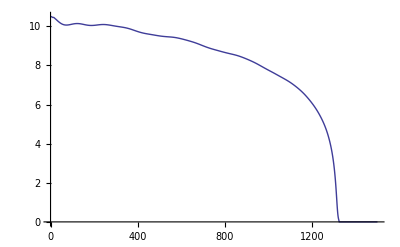

```mathematica
ListLinePlot[ReadMinTrackerRadius["J5.25_17c"]]
```

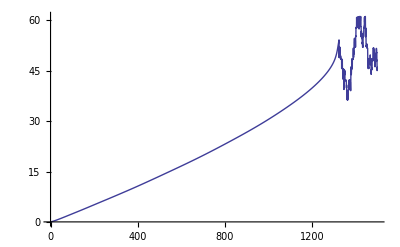

```mathematica
ListLinePlot[ph]
```

```mathematica
Clear[MapThreadData]
```

```mathematica
?MapThreadData
```

Global`MapThreadData

MapThreadData[f_,ds:{DataTable[...]...}]:=Module[{lists,vals,xs,fOfVals},lists=ToList/@ds;vals=DepVar/@ds;xs=IndepVar[First[ds]];fOfVals=MapThread[f,vals];MakeDataTable[xs,fOfVals]]

```mathematica
xpy=MapThreadData[Sqrt[#1^2+#2^2]&,{coordX,coordY}]
```

DataTable[...]

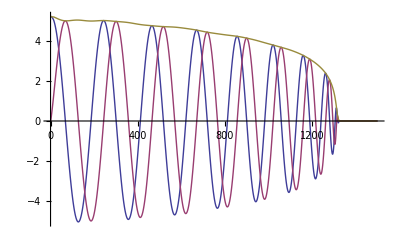

```mathematica
ListLinePlot[{coordX,coordY,xpy}]
```

## Convergence testing

```mathematica
Get["~/projects/nrmma/nrmma.m"]
```

```mathematica
ResolutionCode[n_Integer]:=Module[{},If[!(Mod[n,4]===0),Throw["Number of points must be a multiple of 4"]];
If[n<16,Throw["Number of points must be at least 16"]];
If[n>116,Throw["Number of points must be less than 116"]];
Return[FromCharacterCode[n/4-4+97]]]
```

```mathematica
phases={ph1,ph2,ph3}=Map[ReadMinTrackerPhase["J5.25_17"<>#]&,{"c","d","e"}]
```

Reading...

Reading...

Reading...

«3 more identical outputs»

{DataTable[...],DataTable[...],DataTable[...]}

```mathematica
commonAttributes[cs]
```

{{NPoints→24},{NPoints→28},{NPoints→32}}

{}

```mathematica
namer=ResolutionCode
```

ResolutionCode

```mathematica
cs=LoadConvergenceSeries["J5.25_17",{24,28,32},ReadMinTrackerPhase,namer]
```

Reading...

Reading...

Reading...

«3 more identical outputs»

{DataTable[...],DataTable[...],DataTable[...]}

```mathematica
Map[ListAttributes,cs]
```

{{NPoints→24},{NPoints→28},{NPoints→32}}

```mathematica
RescaledErrors[4,LoadConvergenceSeries["J5.25_17",{24,28,32},ReadMinTrackerPhase,namer]]
```

{DataTable[...],DataTable[...]}

```mathematica
{{0,100},{-1,1}}
```

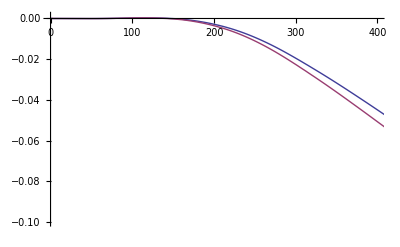

```mathematica
ListLinePlot[RescaledErrors[4,LoadConvergenceSeries["J5.25_17",{24,28,32},ReadMinTrackerPhase,namer]] ,
PlotRange->{{0,400},{-0.1,0.001}} ]
```

```mathematica
Get["~/projects/nrmma/nrmma.m"]
```

```mathematica
cr=ConvergenceRate[LoadConvergenceSeries["J5.25_17",{24,28,32},ReadMinTrackerPhase,namer]]
```

DataTable[...]

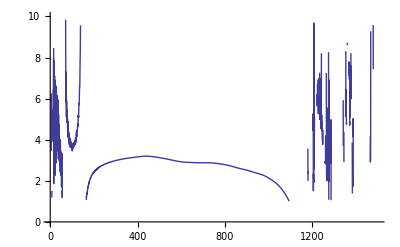

```mathematica
ListLinePlot[cr,PlotRange->{0,10}]
```

```mathematica
csw=LoadConvergenceSeries["J5.25_17",{24,28,32},ReadPsi4[#,2,2,70]&,namer]
```

{1.,0.857143,0.75}

Automatically downsampling

4

{6,7,8}

{DataTable[...],DataTable[...],DataTable[...]}

```mathematica
Map[Spacing, csw]
```

{6.,6.,6.}

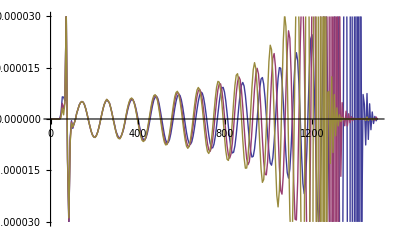

```mathematica
ListLinePlot[Map[MapData[Re,#]&,csw]]
```

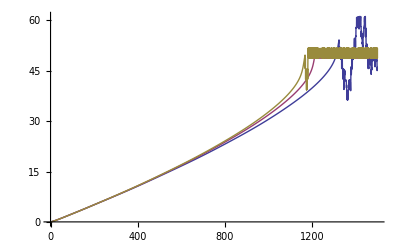

```mathematica
ListLinePlot[cs]
```

```mathematica
Map[Length,phases]
```

{1,1,1}

```mathematica
Length[ph1]
```

4001

```mathematica
?Length
```

RowBox[{"Length", "[", StyleBox["expr", "TI"], "]"}] gives the number of elements in StyleBox["expr", "TI"].

```mathematica
ListLinePlot[phases]
```

-Graphics-

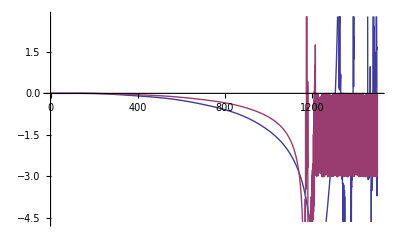

```mathematica
ListLinePlot[{ph1-ph2,ph2-ph3}]
```